## 00+11→T_2^-

### f_1=C ⅇ^(-t/T_2)+D

```mathematica
distr00b={{1,88.6},{3,88.1},{5,85.9},{7,85.1},{9,83.5},{11,83.1},{13,81.4},{15,79.2},{17,79},{19,76.3},{21,74.3},{23,73.4},{25,71.4},{27,68.4},{29,68.8},{31,67.8},{33,63},{35,64.3},{37,61.9},{39,59.6},{41,59.3},{43,58.4},{45,58},{47,55.4},{49,51.4},{51,47.5},{53,46.9},{55,48.7},{57,43.4},{59,43.6},{61,43.5},{63,42.2},{65,42.7},{67,41.6},{69,39.9},{71,39.8},{73,39.2},{74,40.5}};Pt1=C1 Exp[-t/T2]+C3;
```

```mathematica
FindFit[distr00b,Pt1,{C1,T2,C3},t]
```

{C1→169.713,T2→189.013,C3→-78.0434}

```mathematica
fit1=NonlinearModelFit[distr00b,Pt1,{C1,T2,C3},t];Normal[fit1]
```

-78.0434+169.713 ⅇ^(-0.00529065 t)

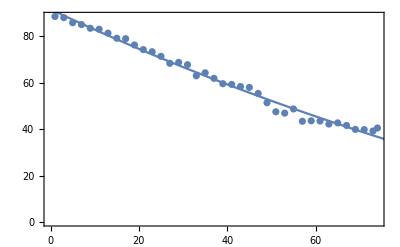

```mathematica
Show[ListPlot[distr00b],Plot[fit1[x],{x,0,80}],Frame->True]
```

Error=1/38∑_(i=1)^38 (f_1(i)-d(i))^2:

```mathematica
error1=fit1["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

2.92664

### f_2=C ⅇ^(-(t/T_2)^2)+D

```mathematica
Pt2=C2 Exp[-(t/T2b)^2]+C4;
FindFit[distr00b,Pt2,{C2,T2b,C4},t]
fit2=NonlinearModelFit[distr00b,Pt2,{C2,T2b,C4},t];Normal[fit2]
```

{C2→50.107,T2b→45.0762,C4→35.8193}

35.8193+50.107 ⅇ^(-0.000492159 t^2)

```mathematica
error2=fit2["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

2.29785

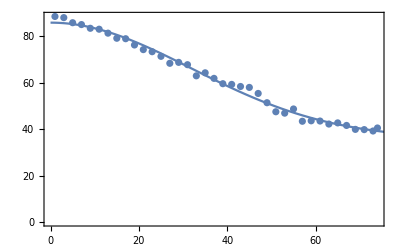

```mathematica
Show[ListPlot[distr00b],Plot[fit2[x],{x,0,80}],Frame->True]
```

### f_3=C t+D

```mathematica
fit3=LinearModelFit[distr00b,t,t]
```

FittedModel[89.7223-0.737594 t]

```mathematica
error3=fit3["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

3.68182

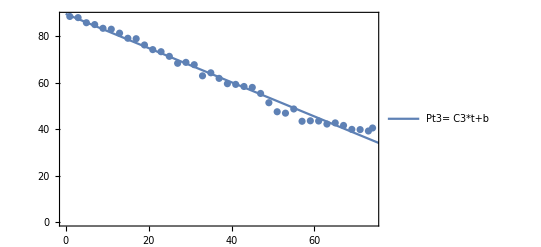

```mathematica
Show[ListPlot[distr00b],Plot[fit3[t],{t,0,80}],Frame->True]
```

## 01+10→T_2^+

### f_1=C ⅇ^(-t/T_2)+D

```mathematica
distr2={{0,88.6},{1,84.7},{3,86.8},{5,85.8},{7,82.7},{9,79.8},{11,83.8},{13,81},{15,79.9},{17,82.2},{19,78.7},{21,77.9},{23,75},{25,72.7},{27,75.9},{29,74.1},{31,75},{33,71.7},{35,70.5},{37,73},{39,72},{41,71.1},{43,69.3},{45,65.5},{47,67.4},{49,66.3},{51,66.1},{53,64.2},{55,62.8},{57,61},{59,61.9},{61,61.9},{63,59.3},{65,59.3},{67,59.7},{69,57.4},{71,57}};
```

```mathematica
FindFit[distr2,Pt1,{C1,T2,C3},t]
fit4=NonlinearModelFit[distr2,Pt1,{C1,T2,C3},t];Normal[fit4]
```

{C1→415.596,T2→951.874,C3→-328.735}

-328.735+415.596 ⅇ^(-0.00105056 t)

```mathematica
error4=fit4["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

2.01425

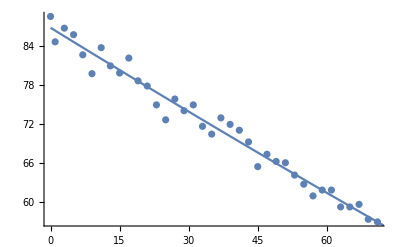

```mathematica
Show[ListPlot[distr2],Plot[fit4[t],{t,0,80},Frame->True]]
```

### f_2=C ⅇ^(-(t/T_2)^2)+D

```mathematica
FindFit[distr2,Pt2,{C2,T2b,C4},t]
fit5=NonlinearModelFit[distr2,Pt2,{C2,T2b,C4},t];Normal[fit5]
```

{C2→29.0724,T2b→47.8111,C4→55.0659}

55.0659+29.0724 ⅇ^(-0.000437465 t^2)

```mathematica
error5=fit5["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

3.22464

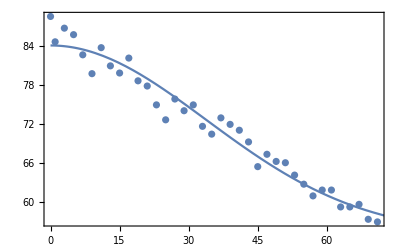

```mathematica
Show[ListPlot[distr2],Plot[fit5[x],{x,0,80}],Frame->True]
```

### f_3=C t+D

```mathematica
fit6=LinearModelFit[distr2,t,t]
```

FittedModel[86.6876-0.420865 t]

```mathematica
error6=fit6["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

2.02206

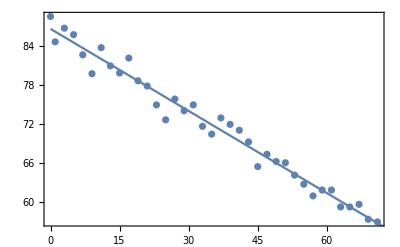

```mathematica
Show[ListPlot[distr2],Plot[fit6[t],{t,0,80}],Frame->True]
```